```mathematica
Quit[]
```

```mathematica
With[{pts={{0,0,0},{1,0,0},{0,1,0},{1,0,1},{0,1,1},{1,1,1}},fcs={{1,2,3},{4,5,6},{1,2,4},{1,3,5},{2,3,6},{1,4,5},{3,5,6},{2,4,6}}},Graphics3D[{Opacity[0.9],Texture[-Graphics-],Polyhedron[pts[[Sequence@#]]&/@fcs,VertexTextureCoordinates->(pts[[Sequence@#]]&/@fcs)]}]]
```

-Graphics3D-

```mathematica
With[{pts={{0,0,0},{1,0,0},{0,1,0},{1,0,1},{0,1,1},{1,1,1}},fcs={{1,2,3},{4,5,6},{1,2,4},{1,3,5},{2,3,6},{1,4,5},{3,5,6},{2,4,6}}},pts[[Sequence@#]]&/@fcs]
```

{{{0,0,0},{1,0,0},{0,1,0}},{{1,0,1},{0,1,1},{1,1,1}},{{0,0,0},{1,0,0},{1,0,1}},{{0,0,0},{0,1,0},{0,1,1}},{{1,0,0},{0,1,0},{1,1,1}},{{0,0,0},{1,0,1},{0,1,1}},{{0,1,0},{0,1,1},{1,1,1}},{{1,0,0},{1,0,1},{1,1,1}}}

```mathematica
Inverse[{{1,0,1},{0,1,1},{1,1,1}}ᵀ]
```

{{0,-1,1},{-1,0,1},{1,1,-1}}

```mathematica
Graphics3D[Arrow[{{0,0,0},#}]&/@(Tuples[{0,1},3].%32)]
```

-Graphics3D-

Are there any arrangement acheiving maximum product except for cube-with-basis? achNumber counts number of such arrangements given a non-degenerate 0-1 matrix -- basis of the second set in the coordinates dual to some basis of the second set. If maximum is only acheived with cube+basis, the function will return 2

```mathematica
$HistoryLength=1
```

1

```mathematica
achNumber[B01_List]:=With[{Cpl=Complement,Len=Length,d=Length@B01,cube=Tuples[{0,1},Length@B01],inv=Inverse[B01]},With[{acan=Select[Subsets[Cpl[cube,B01]],Divisible[2^d(d+1),(Len@#+d)]&],bcan=Select[Subsets[Cpl[cube,B01ᵀ]],Divisible[2^d(d+1),(Len@#+d)]&]},Total@Flatten@Table[Boole[Cpl[Flatten[Join[B01,a].inv.(Join[B01ᵀ,b]ᵀ)],{0,1}]=={}],{a,acan},{b,Select[bcan,Len@#==(2^d(d+1))/(d+Len@a)-d&]}]]]
```

Test on all invertible 2 x2 matrices :

```mathematica
Tally[achNumber/@Select[Tuples[{0,1},{2,2}],MatrixRank@#==2&]]//AbsoluteTiming
```

{0.0036872,{{2,6}}}

Test on all invertible 3x3 matrices:

```mathematica
Tally[achNumber/@Select[Tuples[{0,1},{3,3}],MatrixRank@#==3&]]//AbsoluteTiming
```

{0.140387,{{2,174}}}

Number of 4x4 basises ignoring order:

```mathematica
Select[DeleteDuplicates[Sort/@Tuples[{0,1},{4,4}]],MatrixRank@#==4&]//Length
```

940

```mathematica
achNumber[IdentityMatrix[4]]//AbsoluteTiming
```

{15.8582,2}

```mathematica
35*940/3600.
```

9.13889

```mathematica
SeedRandom[42];fourByFourSample=Transpose/@RandomSample[Select[DeleteDuplicates[Sort/@Tuples[{0,1},{4,4}]],MatrixRank@#==4&],4]
```

{{{0,0,1,1},{0,1,0,0},{1,0,0,1},{1,0,1,0}},{{0,0,0,1},{0,1,1,0},{0,0,1,1},{1,1,0,0}},{{0,0,0,1},{0,0,1,1},{0,1,0,0},{1,1,1,0}},{{0,0,1,1},{0,1,0,1},{0,1,1,0},{1,1,1,0}}}

```mathematica
(achNumber/@fourByFourSample)//AbsoluteTiming
```

{565.683,{2,2,2,2}}

```mathematica
matrixPicture[B01_]:=Module[{d=Length@B01,cube,final,pos1,pos2},cube=Tuples[{0,1},d];pos1=Flatten[Position[cube,#]&/@(B01ᵀ)]; pos2=Flatten[Position[cube,#]&/@B01];final=cube.Inverse@B01.(cubeᵀ);
Style[{ArrayPlot[final,ColorRules->{0->GrayLevel[0],1->RGBColor[0.2, 0.2, 0.2]},ColorFunction->(ColorData["Rainbow",(#+1)/2]&),Epilog->{Black,MapIndexed[Text[#1,Reverse[#2-0.5]]&,Reverse[final],{2}],RGBColor[0.23, 0.94, 1],Arrow[{{#-0.5,2^d},{#-0.5,2^d-1/2}}]&/@pos1,Arrow[{{0,2^d-#+0.5},{0.5,2^d-#+0.5}}]&/@pos2},ImageSize->300,Frame->None,Background->White,PlotRangePadding->0.1],Style[B01//MatrixForm,White]},White,Background->Black]]
```

```mathematica
matrixPicture[{{1,0,1},{0,1,1},{0,0,1}}]//Rasterize
```

-Graphics-

```mathematica
matrixPicture[IdentityMatrix@3]//Rasterize
```

-Graphics-

```mathematica
matrixPicture@First[RandomChoice[Select[Tuples[{0,1},{3,3}],MatrixRank@#==3&],1]]//Rasterize
```

-Graphics-

```mathematica
imlist=Rasterize/@matrixPicture/@Select[Tuples[{0,1},{3,3}],MatrixRank@#==3&];
```

```mathematica
matrixPicture@IdentityMatrix[4]//Rasterize
```

-Graphics-

```mathematica
NestWhile[RandomChoice[{0,1},{4,4}]&,{{0}},MatrixRank[#]!=4&]
```

{{0,1,1,1},{1,0,0,1},{0,1,1,0},{0,1,0,1}}

```mathematica
matrixPicture@%//Rasterize
```

-Graphics-

```mathematica
Inverse@{{0,1,1,1},{1,0,0,1},{0,1,1,0},{0,1,0,1}}
```

{{-1,1,1,0},{-1,0,1,1},{1,0,0,-1},{1,0,-1,0}}

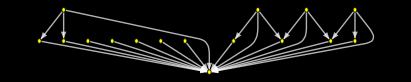

```mathematica
Graph[graphPicture@{{0,1,1,1},{1,0,0,1},{0,1,1,0},{0,1,0,1}},Background->Black,VertexStyle->Yellow,EdgeStyle->White]
```

```mathematica
Graph[graphFullSym@IdentityMatrix[3]]
```

-Graphics-

Check wether sets of “skewed dot products” coincide with all nonbinary inputs treated as same and no distinction between 0 and 1:

```mathematica
coincidingSets[B01_]:=Module[{d=Length@B01,cube,final},cube=Tuples[{0,1},d];final=cube.Inverse@B01.(cubeᵀ)/.{1->0,x_/;x!=0->2};Map[Sort,final,{0,-2}]==Map[Sort,finalᵀ,{0,-2}]]
```

Check on invertible d*d matrices for d from 2 to 4:

```mathematica
Table[And@@coincidingSets/@Select[Tuples[{0,1},{d,d}],MatrixRank@#==d&],{d,2,4}]
```

{True,True,True}

```mathematica
randomInvertible[d_]:=NestWhile[RandomChoice[{0,1},{d,d}]&,{{0}},MatrixRank[#]!=d&]
```

```mathematica
randomInvertible[5]
```

{{1,1,1,0,1},{1,0,0,1,0},{0,1,0,0,0},{1,0,0,1,1},{1,0,0,0,1}}

```mathematica
NotebookDelete[temp]
```

NotebookDelete[temp]

```mathematica
cnt=0;SeedRandom[42];NestWhile[If[Mod[cnt,1]==0,NotebookDelete[temp];temp=PrintTemporary[cnt]];cnt++;randomInvertible[4]&,{{1}},coincidingSets[#]&]
```

$Aborted

```mathematica
counterexample5={{0,0,1,1,1},{0,1,0,0,0},{1,0,0,1,1},{1,1,0,1,0},{1,0,0,0,0}}
```

{{0,0,1,1,1},{0,1,0,0,0},{1,0,0,1,1},{1,1,0,1,0},{1,0,0,0,0}}

```mathematica
coincidingSets@counterexample5
```

False

```mathematica
matrixPicture@counterexample5//Rasterize
```

-Graphics-

```mathematica
cube01[d_]:=Tuples[{0,1},d]
```

```mathematica
Style[With[{cube=Tuples[{0,1},5]},ArrayPlot[Map[Sort,(cube.Inverse[#].(cubeᵀ))/.{1->0,x_/;x!=0->2},{0,-2}],Frame->True,FrameStyle->White,Background->Black,PlotRangePadding->None,Mesh->True,MeshStyle->Directive[GrayLevel[0.27],Thickness[10^-4]],ColorRules->{0->Black,2->Orange}]]&/@{counterexample5,counterexample5ᵀ},White,Background->Black]//Rasterize
```

-Graphics-

```mathematica
Inverse@counterexample5
```

{{0,0,0,0,1},{0,1,0,0,0},{1,0,-1,0,1},{0,-1,0,1,-1},{0,1,1,-1,0}}

Function to produce graph of allowable relations given symmetric invertible 01 matrix:

```mathematica
graphFullSym[B01_]:=Module[{d=Length@B01,cube,matr},cube=Tuples[{0,1},d];matr=(cube.Inverse@B01.(cubeᵀ))/.{1->0,x_/;x!=0->2};
Flatten@Table[If[i!=j&&And@@NonNegative[matr[[i]]-matr[[j]]],cube[[i]]->cube[[j]],Nothing],{i,2^d},{j,2^d}]]
```

All symmetric invertible (without row permutations!) :

```mathematica
allSymInvertible[d_]:=DeleteDuplicatesBy[Select[(#+LowerTriangularize[#ᵀ,-1])&/@PadLeft/@(Internal`PartitionRagged[#,Range[d,1,-1]]&)/@Tuples[{0,1},(d(d+1))/2],MatrixRank@#==d&],Sort]
```

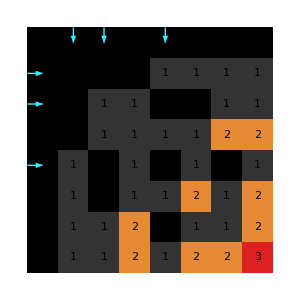
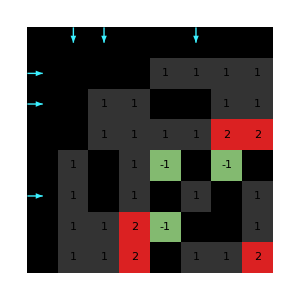
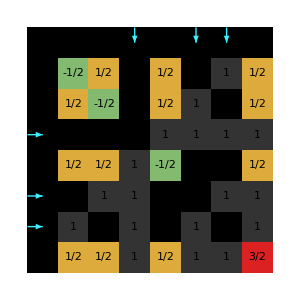
-Graphics- | {-Graphics-,(0 | 0 | 1
0 | 1 | 0
1 | 0 | 0)}
-Graphics- | {-Graphics-,(0 | 0 | 1
0 | 1 | 0
1 | 0 | 1)}
-Graphics- | {-Graphics-,(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)}

```mathematica
Style[Grid@DeleteDuplicates[{Graph[graphFullSym@#,Background->Black,VertexStyle->White,EdgeStyle->Yellow],matrixPicture@#}&/@allSymInvertible[3],IsomorphicGraphQ[#1[[1]],#2[[1]]]&],Background->Black,White]
```

```mathematica
Inverse@({{0, 0, 1}, {0, 1, 0}, {1, 0, 1}})
```

{{-1,0,1},{0,1,0},{1,0,0}}

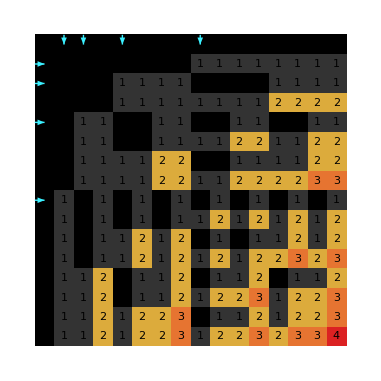
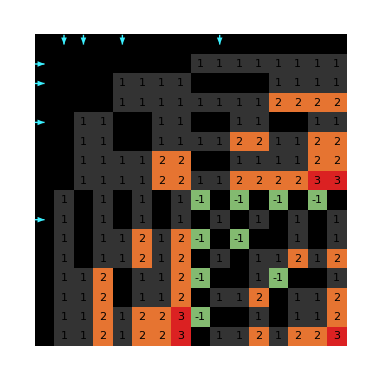
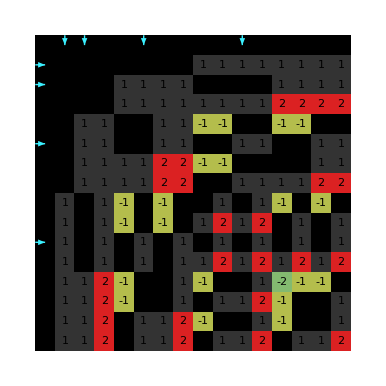
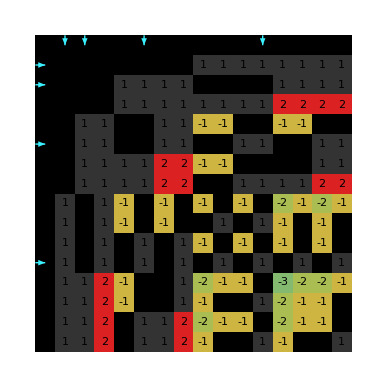
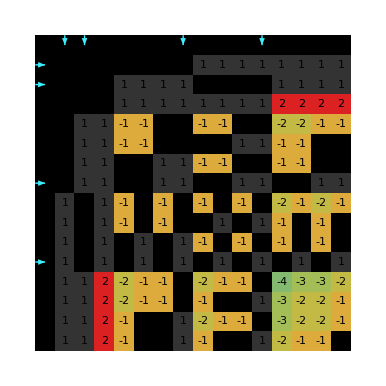
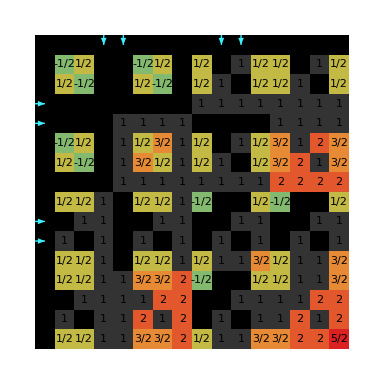
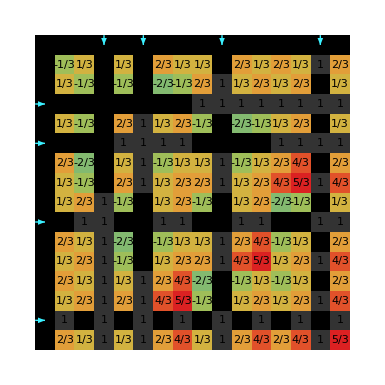
-Graphics- | {-Graphics-,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}
-Graphics- | {-Graphics-,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 1)}
-Graphics- | {-Graphics-,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0)}
-Graphics- | {-Graphics-,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 1)}
-Graphics- | {-Graphics-,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 1 | 1
1 | 0 | 1 | 1)}
-Graphics- | {-Graphics-,(0 | 0 | 1 | 1
0 | 1 | 0 | 0
1 | 0 | 0 | 1
1 | 0 | 1 | 0)}
-Graphics- | {-Graphics-,(0 | 0 | 1 | 1
0 | 1 | 0 | 1
1 | 0 | 0 | 1
1 | 1 | 1 | 0)}

```mathematica
Style[Grid@DeleteDuplicates[{Graph[graphFullSym@#,Background->Black,VertexStyle->White,EdgeStyle->Yellow],matrixPicture@#}&/@allSymInvertible[4],IsomorphicGraphQ[#1[[1]],#2[[1]]]&],Background->Black,White]
```

```mathematica
{Graph[graphFullSym[counterexample5]],Graph[graphFullSym[counterexample5ᵀ]]}
```

{-Graphics-,-Graphics-}

```mathematica
graphSymNoSinks[B01_]:=Module[{d=Length@B01,filtcube,matr,pos},filtcube=Rest@DeleteCases[Tuples[{0,1},d],Alternatives@@B01];matr=(filtcube.Inverse@B01.(filtcubeᵀ))/.{1->0,x_/;x!=0->2};
Flatten@Table[If[i!=j&&And@@NonNegative[matr[[i]]-matr[[j]]],filtcube[[i]]->filtcube[[j]],Nothing],{i,2^d-d-1},{j,2^d-d-1}]]
```

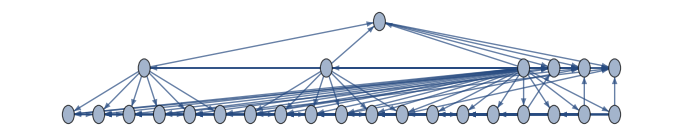

```mathematica
Graph[graphSymNoSinks@IdentityMatrix@5,GraphLayout->"LayeredEmbedding"]
```

```mathematica
graphSymFactorizedAndSzs[B01_]:=Module[{d=Length@B01,cube,grps,filt=(#/.{1->0,x_/;x!=0->2}&)},cube=Tuples[{0,1},d];grps={#,filt[#[[1]]]}&/@GatherBy[cube.Inverse@B01.(cubeᵀ),filt];
{Flatten@Table[If[i!=j&&And@@NonNegative[grps[[i,2]]-grps[[j,2]]],grps[[i,1]]->grps[[j,1]],Nothing],{i,Length@grps},{j,Length@grps}],Normal@AssociationMap[Length,grps[[All,1]]]}]
```

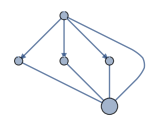

```mathematica
With[{gsf=graphSymFactorizedAndSzs[IdentityMatrix[3]]},Graph[First@gsf,VertexLabels->MapAt[Placed[#,Center]&,gsf[[2]],{All,2}],VertexSize->MapAt[{"Scaled",Sqrt[#]/20}&,gsf[[2]],{All,2}]]]
```

```mathematica
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]
```

The currently installed versions of IGraph/M are: {}

Installing IGraph/M is complete: PacletObject[…].

It can now be loaded using the command <<IGraphM`

```mathematica
<<IGraphM`
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

```mathematica
Remove[Global`IGVertexMap]
Remove[Global`IGVertexProp]
```

```mathematica
graphSymFactorizedRaw[B01_]:=Module[{d=Length@B01,cube,grps,filt=(#/.{1->0,x_/;x!=0->2}&)},cube=Tuples[{0,1},d];grps={#,filt[#[[1]]]}&/@GatherBy[cube.Inverse@B01.(cubeᵀ),filt];
Flatten@Table[If[i!=j&&And@@NonNegative[grps[[i,2]]-grps[[j,2]]],grps[[i,1]]->grps[[j,1]],Nothing],{i,Length@grps},{j,Length@grps}]]
hasseDiagram[gr_]:=With[{f=EdgeQ[gr,#1->#2]&,s=VertexList[gr]},ResourceFunction["HasseDiagram"][f,s,PerformanceGoal->"Quality"]]
```

```mathematica
addGraphProps[gr_]:=Module[{filt=(#/.{1->0,x_/;x!=0->2}&)},gr//IGVertexMap[Sqrt@*Length,"SqLength"->VertexList]/*IGVertexMap[Length,"Length"->VertexList]/*IGVertexMap[filt[#[[1]]]&,"Filter"->VertexList]/*IGVertexMap[MatrixForm[#ᵀ]&,Tooltip->VertexList]]
grSymFact[B01_]:=addGraphProps[Graph[graphSymFactorizedRaw[B01],PerformanceGoal->"Quality"]]
hasseSymFact[B01_]:=addGraphProps[hasseDiagram@Graph[graphSymFactorizedRaw[B01],PerformanceGoal->"Speed"]]
```

```mathematica
dispFact[gr_]:=gr//IGVertexMap[0.1#&,VertexSize->IGVertexProp["SqLength"]]/*IGVertexMap[Placed[If[#==1,"",#],Center]&,VertexLabels->IGVertexProp["Length"]]
```

```mathematica
dispFact[grSymFact[#]]&/@allSymInvertible[3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

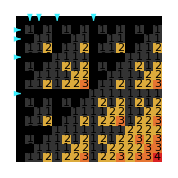
{-Graphics-,(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

```mathematica
matrixPicture@IdentityMatrix[4]
```

```mathematica
dispFact[grSymFact[IdentityMatrix[4]]]
```

-Graphics-

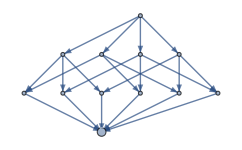

```mathematica
dispFact[hasseSymFact[IdentityMatrix@4]]
```

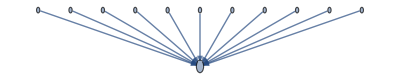
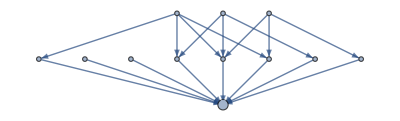
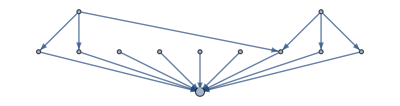
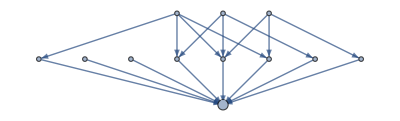
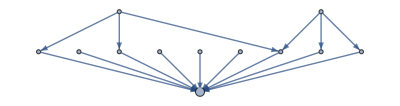
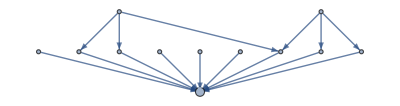
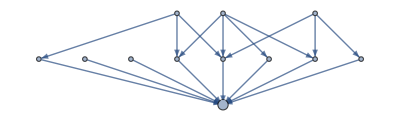
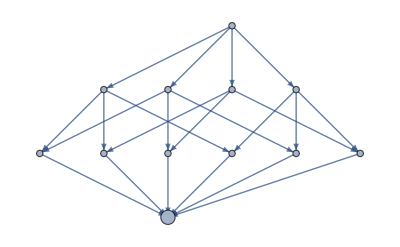
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(dispFact@*hasseSymFact)/@RandomSample[allSymInvertible[4],30]
```

```mathematica
deepSort[expr_]:=Map[Sort,expr,{0,-2}]
```

```mathematica
allSymInvertibleDiffGraph[d_]:=First/@DeleteDuplicates[{#,Graph@graphFullSym@#}&/@allSymInvertible[d],IsomorphicGraphQ[#1[[2]],#2[[2]]]&]
```

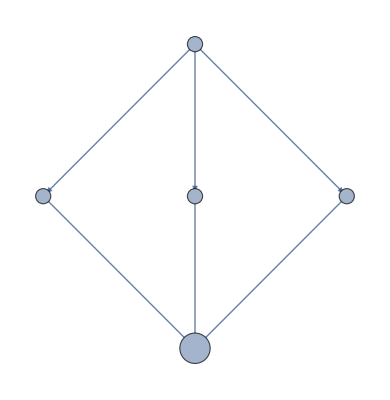
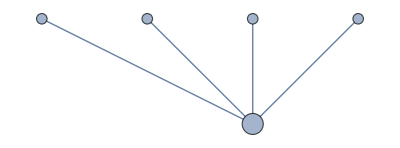
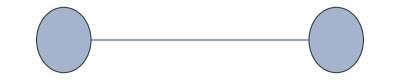

```mathematica
allThreeHasse=dispFact/@hasseSymFact/@allSymInvertibleDiffGraph[3]
```

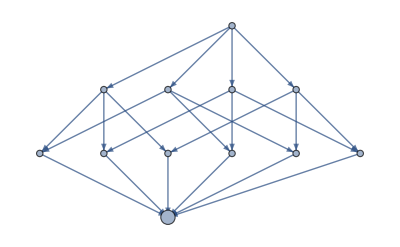
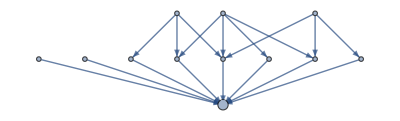
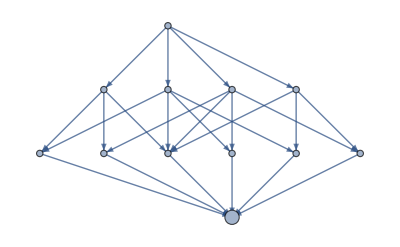
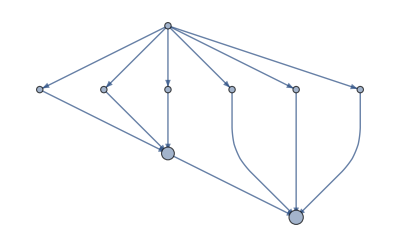
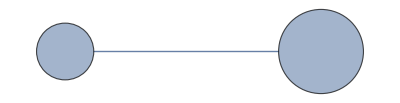
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
allFourHasse=dispFact/@hasseSymFact/@allSymInvertibleDiffGraph[4]
```

```mathematica
setGraphStyle[graph_Graph]:=Graph[graph,EdgeStyle->Yellow,VertexStyle->White,Background->Black,PerformanceGoal->"Quality"]
```

```mathematica
Grid[ArrayReshape[setGraphStyle/@(allFourHasse~Join~allThreeHasse),{5,2}],Background->Black]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"All-Hasse-3-4-diagrams.jpg"}],-Graphics-];
```

```mathematica
allHasse5withDup=ParallelMap[hasseSymFact,allSymInvertible[5]];
```

```mathematica
allFiveHasse=DeleteDuplicates[allHasse5withDup,IsomorphicGraphQ];
```

```mathematica
Grid[ArrayReshape[setGraphStyle/@(allFourHasse~Join~allThreeHasse),{5,2}],Background->Black]
```

```mathematica
DumpSave[FileNameJoin[{NotebookDirectory[],"all-sym-hasse-3.mx"}],allThreeHasse];DumpSave[FileNameJoin[{NotebookDirectory[],"all-sym-hasse-4.mx"}],allFourHasse];DumpSave[FileNameJoin[{NotebookDirectory[],"all-sym-hasse-5.mx"}],allFiveHasse];
```

```mathematica
MapIndexed[Export[FileNameJoin[{NotebookDirectory[],"all-sym-hasse-5-pictures",ToString[#2[[1]]]<>".jpg"}],#1]&,setGraphStyle[Graph[dispFact@#,ImageSize->800]]&/@allFiveHasse];
```

There is an example that is not even a semilattice among 4 by 4 matrices

```mathematica
nonSemilatticecCounter=allSymInvertibleDiffGraph[4][[4]]
```

{{0,0,0,1},{0,0,1,0},{0,1,0,1},{1,0,1,1}}

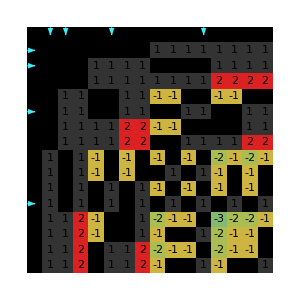
{{-Graphics-,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 1)},(-1 | -1 | 0 | 1
-1 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),-Graphics-}

```mathematica
Style[{matrixPicture[nonSemilatticecCounter],Style[MatrixForm@Inverse@nonSemilatticecCounter,White],Graph[setGraphStyle@dispFact@hasseSymFact@nonSemilatticecCounter,ImageSize->400]},Background->Black]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"non-semilattice-4.jpg"}],%];
```

```mathematica
With[{c=cube01[4],ctr=Inverse@nonSemilatticecCounter},{MatrixForm[c.ctr.(cᵀ)],MatrixForm@c,MatrixForm@ctr,MatrixForm@(cᵀ)}]
```

Unlike the simple cube case there might be more then d+1 vectors that can lie in intersection (meet) of A and B; the following function counts the number of such vectors.

```mathematica
selfCompatibleCount[B01_]:=With[{c=Tuples[{0,1},Length@B01]},Count[Diagonal[c.Inverse[B01].(cᵀ)],0|1]]
```

```mathematica
Union[selfCompatibleCount/@allSymInvertible[3]]
```

{4,6}

```mathematica
Union[selfCompatibleCount/@allSymInvertible[4]]
```

{5,6,8,9,10}

```mathematica
Union[selfCompatibleCount/@allSymInvertible[5]]
```

{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,24}

In case of 4 by 4 matrices numbers of possible self-compatible vectors reduces when only considering matrices that produce non-isomorphic graphs. So there are matrices producing isomorphic graphs but having different-sized self-compatible sets.

A matrix with many self - compatible vecrors:

```mathematica
manySelfCompatibleExample=Select[allSymInvertible[5],selfCompatibleCount@#==24&,1]//First
```

{{0,0,0,1,1},{0,1,1,0,1},{0,1,1,1,0},{1,0,1,0,0},{1,1,0,0,1}}

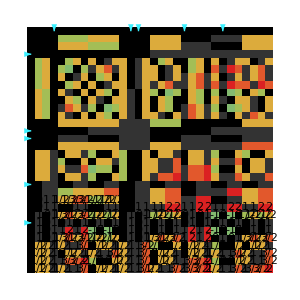
{{-Graphics-,(0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1)},-Graphics-}5×5 matrix producing 24 self-compatible vectors

```mathematica
Labeled[Style[{matrixPicture[manySelfCompatibleExample],Graph[setGraphStyle@dispFact@hasseSymFact@manySelfCompatibleExample,ImageSize->550]},Background->Black],Style["5×5 matrix producing 24 self-compatible vectors",White,Background->Black],Top]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"many-self-compatible-example.jpg"}],%345,Background->Black];
```

```mathematica
matrixPicture@allSymInvertible[4][[1]]
```

{-Graphics-,(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
matrixPicture@IdentityMatrix[4]
```

{-Graphics-,(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

```mathematica
IsomorphicSubgraphQ@@(Graph/@graphFullSym/@{IdentityMatrix[4],Reverse[IdentityMatrix[4]]})
```

True

```mathematica
allSymPermutations[d_]:=Select[PermutationMatrix/@Permutations[Range@d],SymmetricMatrixQ]
```

```mathematica
dispFact@addGraphProps@hasseSymFact@#&/@{IdentityMatrix[4],Reverse[IdentityMatrix[4]]}
```

{-Graphics-,-Graphics-}

```mathematica
posSelfComp3=With[{as3p=allSymPermutations[3],as3in=allSymInvertible[3]},(m|->Sort[selfCompatibleCount/@(m.#&/@as3p)])/@as3in];
```

```mathematica
possibleSelfCompCountsGrouped3=SortBy[Tally[posSelfComp3],First]
```

{{{4,4,4,4},1},{{4,6,7,7},4},{{5,6,6,7},12},{{5,6,7,8},6}}

```mathematica
posSelfComp4=With[{as4p=allSymPermutations[4],as4in=allSymInvertible[4]},(m|->Sort[selfCompatibleCount/@(m.#&/@as4p)])/@as4in];
```

```mathematica
possibleSelfCompCountsGrouped4=SortBy[Tally[posSelfComp4],First]
```

{{{5,5,5,5,5,5,5,5,5,5},1},{{5,5,5,5,8,8,8,8,8,8},4},{{5,5,6,7,7,7,7,8,8,8},4},{{5,9,9,9,9,9,11,11,11,11},1},{{5,9,9,9,10,10,10,12,12,12},4},{{6,6,6,8,10,10,10,12,12,12},4},{{6,6,7,7,8,10,10,11,11,12},24},{{6,6,8,8,8,10,12,12,12,12},12},{{6,10,10,10,10,12,12,12,12,12},12},{{6,10,10,12,12,13,14,14,15,16},24},{{7,9,9,10,10,10,11,11,12,13},24},{{7,9,9,10,10,11,11,11,14,14},3},{{7,9,9,11,11,11,12,12,12,12},9},{{7,9,10,12,12,12,13,13,14,14},24},{{7,10,10,10,10,11,12,12,14,14},9},{{7,10,10,11,12,12,12,12,12,12},3},{{8,9,10,10,10,11,12,12,14,14},24},{{8,10,10,10,11,12,12,13,14,14},24},{{8,10,10,11,11,12,14,14,14,14},24},{{9,9,9,10,10,10,11,11,11,12},48},{{9,9,10,10,10,10,11,11,11,11},12},{{9,9,10,10,10,11,11,12,12,12},24},{{9,9,10,10,10,11,11,12,12,14},6},{{9,9,10,10,11,11,11,11,12,14},24},{{10,10,10,10,10,10,11,11,12,12},12},{{10,10,10,10,11,11,12,14,14,14},12}}

```mathematica
posSelfComp5=With[{as5p=allSymPermutations[5],as5in=allSymInvertible[5]},ParallelMap[m|->Sort[selfCompatibleCount/@(m.#&/@as5p)],as5in]];
```

```mathematica
possibleSelfCompCountsGrouped5=SortBy[Tally[posSelfComp5],First]
```

{{{6,6,6,6,6,6,6,6,9,9,9,9,9,9,9,9,9,9,9,9,11,11,11,11,11,11},10},{{6,6,6,6,6,6,6,8,8,10,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15},5},{{6,6,6,6,8,8,8,8,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,11,11},30},{{6,6,6,6,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10},20},{{6,6,6,8,8,8,8,8,8,10,13,13,13,13,13,13,13,13,13,13,13,13,15,15,15,15},5},{{6,6,6,8,8,8,8,9,9,9,9,9,9,9,9,10,10,10,10,10,11,11,11,11,11,11},12},{{6,6,8,12,12,12,12,12,12,14,14,14,15,15,18,18,18,18,18,20,20,20,21,21,23,23},20},{{6,7,7,8,8,8,8,9,10,10,10,11,11,12,12,12,12,13,13,13,14,14,14,14,15,15},45},{{6,7,7,8,11,12,12,12,13,13,14,14,14,14,14,14,14,14,14,14,14,15,15,15,16,16},60},{{6,8,8,8,8,8,9,9,9,9,9,10,10,10,10,10,12,12,12,12,12,13,13,13,13,13},3},{{6,8,8,8,8,9,9,9,10,12,12,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14},15},{{6,8,9,10,10,10,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,13,13,13},9},{{6,12,12,12,12,12,12,12,12,12,12,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14},1},{{6,12,12,12,12,12,12,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,21,21,21,21},5},{{6,12,12,15,15,15,15,18,18,18,18,18,18,18,21,21,21,21,21,21,21,21,21,21,21,21},1},{{7,7,7,9,9,10,10,13,13,13,13,14,14,14,14,15,15,15,15,15,16,16,16,16,16,16},20},{{7,7,8,8,8,8,9,9,9,9,9,11,11,12,12,13,13,13,14,14,14,14,14,14,15,15},60},{{7,8,8,8,8,8,8,10,10,10,10,11,11,11,15,15,15,15,15,15,15,15,15,15,15,15},20},{{7,8,8,8,9,9,9,9,9,9,10,10,10,13,13,13,13,13,13,13,13,13,16,16,16,16},20},{{7,8,12,13,13,13,13,13,13,14,14,14,15,15,15,17,18,18,19,19,20,20,20,22,22,23},120},{{7,9,9,9,10,10,10,12,12,13,13,13,13,14,14,14,14,14,14,15,15,16,16,16,16,16},120},{{7,9,9,10,10,10,10,12,12,12,12,12,12,12,13,14,14,14,14,14,15,15,15,15,15,15},20},{{7,15,15,16,16,17,17,18,18,18,19,19,19,20,20,21,21,22,22,24,26,26,26,28,28,28},60},{{7,15,15,17,19,19,19,19,19,19,19,19,19,21,21,21,21,21,21,21,21,21,21,21,23,23},20},{{8,8,8,8,9,9,9,11,11,12,12,13,13,13,13,13,13,14,14,14,14,14,15,15,15,16},120},{{8,8,8,12,12,12,12,12,14,14,14,14,17,17,18,18,18,19,19,20,20,20,20,22,23,23},60},{{8,8,8,12,12,12,12,12,16,16,16,16,16,16,17,17,17,17,17,17,20,20,20,20,20,20},10},{{8,8,9,9,9,10,11,11,11,12,13,13,13,13,13,13,14,14,14,14,14,14,15,15,15,15},120},{{8,8,10,10,11,11,11,11,12,12,13,13,14,14,14,14,15,15,15,15,15,15,16,16,16,16},45},{{8,8,11,11,11,11,12,12,12,13,13,13,13,14,14,14,14,14,14,15,15,15,15,16,16,20},30},{{8,10,10,10,11,11,12,12,14,15,16,16,17,17,18,18,18,19,19,20,20,20,20,20,20,21},120},{{8,10,10,10,12,12,12,14,14,14,15,15,16,16,17,17,18,18,18,18,18,18,19,19,20,20},60},{{8,10,10,10,12,13,13,14,17,17,18,18,18,18,18,19,19,20,20,20,20,20,20,20,20,22},60},{{8,10,10,12,12,13,13,13,14,16,18,18,19,19,20,20,21,21,22,22,23,24,24,24,24,24},120},{{8,10,10,12,12,13,13,14,14,18,18,20,20,20,20,20,21,21,21,21,21,21,22,22,22,22},45},{{8,10,12,12,12,13,13,14,15,15,16,20,20,20,20,20,20,20,21,21,21,21,24,24,24,24},45},{{8,10,12,12,12,13,13,14,16,17,17,18,18,18,18,19,19,19,19,20,20,20,20,20,22,22},15},{{8,10,12,12,14,14,14,14,14,14,16,18,20,20,20,20,21,21,21,21,22,22,23,23,24,24},60},{{8,11,11,12,12,12,12,14,14,16,16,19,19,20,20,20,20,20,21,21,21,21,24,24,24,24},15},{{8,12,12,12,12,12,14,14,14,14,16,16,16,16,20,20,20,20,20,20,21,21,21,21,21,21},30},{{8,12,12,12,13,14,14,14,14,15,15,16,16,16,16,17,17,18,18,20,22,22,22,23,24,24},120},{{8,12,13,14,15,16,17,18,19,21,21,21,21,22,22,22,22,23,23,24,24,24,24,24,24,24},120},{{8,12,13,17,18,18,18,18,18,18,19,19,19,19,19,19,21,21,21,21,21,21,22,22,25,25},60},{{8,16,16,20,20,20,20,20,20,20,20,20,20,24,24,24,24,24,28,28,28,28,28,28,32,32},15},{{8,16,16,20,20,20,20,22,22,22,22,22,22,22,22,22,22,22,22,22,22,24,24,24,26,26},45},{{8,18,18,18,18,20,20,20,20,22,22,22,22,24,24,24,24,24,26,26,28,28,28,28,30,30},45},{{8,18,18,20,20,20,20,20,20,22,22,22,22,22,22,22,22,22,22,24,24,24,24,24,24,24},15},{{9,10,10,10,10,10,10,12,12,12,12,12,12,13,13,13,13,13,13,13,14,14,14,14,15,15},15},{{9,10,10,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,14,14},45},{{9,10,10,12,12,12,14,14,14,14,14,14,16,16,16,17,18,19,19,22,22,22,23,23,24,24},120},{{9,10,11,12,12,12,14,14,14,15,16,16,16,16,16,17,18,19,19,19,20,21,22,22,22,22},120},{{9,10,12,12,12,12,12,13,14,16,17,19,20,20,20,20,20,21,21,21,21,22,24,24,24,24},120},{{9,15,16,16,17,18,19,20,20,20,21,22,22,22,23,24,24,24,24,24,25,26,26,26,27,30},120},{{9,15,16,18,18,19,19,19,19,20,20,20,20,20,20,21,21,22,22,22,22,23,25,26,26,28},120},{{9,15,18,19,19,19,20,20,20,21,21,21,22,22,22,22,22,22,22,22,22,23,23,24,26,26},60},{{10,10,10,12,12,12,12,12,12,14,16,18,18,19,19,20,20,20,20,20,20,20,21,21,23,23},20},{{10,10,10,12,12,12,12,14,14,14,16,16,16,17,17,17,17,17,17,20,20,20,20,20,20,20},20},{{10,10,10,12,12,12,12,14,14,14,17,17,17,17,17,17,22,22,22,22,22,22,24,24,24,24},20},{{10,10,10,12,12,12,12,16,16,16,16,19,19,19,19,19,19,20,20,20,20,20,20,22,22,22},20},{{10,10,11,11,11,11,11,11,12,14,16,17,17,17,17,17,17,17,17,18,19,19,19,19,20,20},60},{{10,10,11,11,11,12,12,13,16,16,16,17,17,18,18,18,18,19,19,19,19,19,19,20,20,22},120},{{10,10,11,11,12,12,12,12,12,12,13,13,13,13,14,14,14,14,14,14,15,15,15,15,15,15},15},{{10,10,12,12,12,12,12,12,14,14,16,16,16,16,17,18,18,19,19,19,20,20,20,21,21,22},120},{{10,10,12,12,12,12,12,13,13,14,14,14,16,17,17,18,18,18,19,19,20,20,20,20,20,20},60},{{10,11,11,11,11,11,12,13,13,14,16,16,16,17,18,19,20,20,20,20,20,20,20,21,22,24},120},{{10,11,11,11,11,12,12,12,12,13,14,14,15,16,17,17,18,19,19,19,19,20,20,20,21,23},120},{{10,11,11,11,11,12,12,14,14,15,16,17,17,18,19,19,19,20,20,20,20,20,20,21,21,24},120},{{10,11,11,11,11,12,12,14,14,16,16,16,16,16,16,16,17,17,18,19,19,20,20,20,21,21},60},{{10,11,11,11,12,12,12,12,12,12,12,13,14,15,16,16,17,18,18,18,18,19,19,20,21,21},120},{{10,11,11,12,12,12,13,13,14,14,14,16,16,16,17,17,19,19,19,19,20,20,20,20,20,20},60},{{10,12,12,12,12,12,12,12,12,13,14,14,16,16,17,18,20,20,20,20,20,20,21,21,23,23},120},{{10,12,12,12,12,12,12,12,12,14,15,15,16,16,16,19,19,20,20,20,20,20,20,20,23,23},60},{{10,13,13,14,14,16,17,17,18,18,18,19,19,19,19,20,20,20,20,20,20,20,21,21,22,22},120},{{10,13,13,14,17,18,19,19,20,20,20,20,21,21,21,21,21,22,22,22,22,22,23,23,24,24},120},{{10,15,17,18,19,19,20,20,20,20,21,22,22,22,22,22,22,22,23,23,23,24,26,26,26,28},120},{{10,16,16,18,18,18,18,19,19,19,20,20,21,21,21,21,22,22,22,22,22,22,22,23,24,24},120},{{10,16,16,18,18,19,19,19,20,20,21,21,22,22,22,22,22,23,23,23,28,28,28,28,28,28},120},{{10,18,18,20,20,20,20,20,22,22,22,22,22,22,24,24,24,24,24,24,26,26,26,26,26,28},120},{{11,11,11,11,12,12,12,12,12,14,14,14,14,14,14,15,15,15,15,15,15,15,15,16,16,20},30},{{11,11,11,11,12,12,12,12,13,13,13,13,13,13,13,13,14,14,14,14,14,14,15,15,15,15},60},{{11,11,12,12,12,12,13,13,15,16,16,16,17,17,17,17,18,19,19,19,20,20,20,20,20,22},120},{{11,11,12,12,12,12,14,14,15,15,16,20,20,20,20,20,20,20,20,20,20,20,21,21,24,24},60},{{11,11,12,13,13,13,13,14,14,14,15,15,15,15,17,17,17,17,18,18,19,19,22,22,24,30},30},{{11,12,12,12,12,12,12,15,15,16,17,18,18,20,20,20,20,20,20,20,21,22,22,23,24,24},120},{{11,12,14,14,15,15,15,15,15,16,16,16,17,17,17,18,18,18,19,19,19,20,20,20,21,21},60},{{11,13,14,14,15,15,15,15,16,16,16,16,17,18,18,19,20,20,20,21,21,21,21,22,22,24},60},{{11,13,15,15,15,16,16,16,16,17,18,18,18,18,18,18,18,18,20,20,20,20,21,21,22,22},120},{{11,15,15,16,16,18,18,18,19,19,20,20,20,21,21,22,22,22,22,22,22,23,24,24,24,26},120},{{11,15,16,18,18,18,19,19,19,20,20,20,20,21,21,22,22,22,22,22,22,23,24,24,24,26},120},{{11,15,16,18,19,19,20,20,20,20,22,22,22,23,23,24,24,24,25,25,26,26,28,28,28,28},120},{{12,12,12,12,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15},5},{{12,12,12,14,15,15,15,15,15,15,16,16,17,17,17,17,17,18,18,18,18,18,18,18,20,21},120},{{12,12,13,13,18,18,19,19,19,19,19,19,20,20,20,20,21,21,22,22,22,22,23,23,24,24},60},{{12,12,14,15,15,16,16,16,16,16,16,16,17,17,17,17,17,17,18,18,18,19,19,20,21,21},60},{{12,12,14,16,16,16,18,18,20,20,20,20,22,24,24,24,26,26,26,26,26,26,28,28,28,28},60},{{12,12,14,16,17,17,17,17,18,18,18,18,18,19,19,20,20,20,20,20,21,21,21,21,21,21},45},{{12,12,14,16,17,17,18,19,19,19,19,20,21,21,21,21,24,24,24,24,24,24,24,24,25,25},15},{{12,12,14,16,18,18,18,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,21,21,22,22},15},{{12,12,14,16,18,20,20,20,20,20,20,20,20,20,22,22,22,22,24,24,24,24,26,26,26,26},45},{{12,12,15,16,16,18,18,18,18,18,18,20,20,21,21,21,21,21,21,22,22,22,22,23,24,24},60},{{12,12,16,18,19,19,19,20,20,20,20,21,21,22,22,22,23,23,23,24,24,24,28,28,30,30},120},{{12,13,13,14,14,15,15,15,15,16,16,16,17,17,17,17,17,18,18,18,19,20,20,20,21,21},60},{{12,13,13,16,16,16,16,17,18,18,18,20,20,20,20,20,20,20,21,21,21,22,22,22,23,23},20},{{12,13,14,14,16,16,16,16,16,16,16,17,17,17,17,17,17,17,18,18,19,19,19,19,20,20},60},{{12,13,16,18,18,18,18,19,19,19,19,20,20,20,20,20,21,21,21,21,21,21,22,22,22,23},120},{{12,14,14,14,16,16,16,16,18,18,18,18,18,18,20,20,20,20,20,20,22,22,24,28,28,30},30},{{12,14,14,17,18,19,19,20,20,20,20,20,21,21,21,21,21,22,22,22,24,24,24,24,24,24},60},{{12,14,16,16,16,16,16,17,17,18,18,18,19,19,19,19,19,20,20,20,20,20,22,22,23,24},120},{{12,15,15,15,15,16,16,17,17,17,17,17,17,17,17,18,18,18,18,19,19,19,19,20,20,20},30},{{12,15,15,16,17,17,18,18,18,18,18,19,20,20,20,20,20,20,21,21,21,22,23,24,24,25},120},{{12,15,16,17,18,19,19,19,19,20,20,20,20,21,22,22,22,22,22,22,23,24,24,24,26,28},120},{{12,15,16,17,19,19,20,20,20,20,20,21,22,22,22,22,22,23,23,23,24,24,24,24,28,30},120},{{12,15,18,19,19,20,20,20,20,21,21,21,21,22,22,22,22,22,23,24,24,24,24,26,28,30},120},{{12,16,16,17,17,17,17,17,17,17,17,18,18,18,18,18,18,19,20,20,21,21,22,22,23,24},120},{{12,16,16,18,20,20,20,20,20,20,20,22,22,22,22,22,22,24,24,24,24,24,24,24,28,30},120},{{12,16,18,18,19,19,19,20,21,21,21,21,22,22,22,22,22,22,22,23,24,24,24,24,24,26},120},{{12,16,18,20,20,20,20,20,20,20,20,22,22,22,22,22,22,22,24,24,24,24,26,26,28,28},120},{{12,16,18,20,20,20,22,22,22,22,22,22,22,22,24,24,24,24,24,24,24,24,26,26,28,30},120},{{12,16,18,20,20,22,22,22,22,22,22,22,22,22,24,24,24,24,26,28,28,28,28,28,30,32},120},{{13,13,13,14,15,15,17,17,17,19,19,19,19,20,21,21,21,22,22,23,23,24,24,24,25,26},120},{{13,14,14,14,15,15,15,15,15,15,16,16,16,16,17,17,17,17,17,18,18,18,18,18,18,18},60},{{13,14,14,15,16,16,16,16,16,16,17,17,17,19,19,19,20,20,20,20,20,20,21,21,21,21},60},{{13,14,15,15,15,16,16,16,16,16,17,17,17,18,18,18,18,19,19,19,20,20,20,21,21,22},120},{{13,14,15,16,17,18,18,18,18,18,18,20,20,20,20,20,21,21,21,22,22,22,23,24,25,28},120},{{13,14,15,16,18,18,18,18,19,20,20,20,20,21,21,22,22,22,23,23,24,24,24,24,25,28},120},{{13,14,15,17,18,18,19,20,20,20,21,22,22,22,22,22,22,22,23,23,24,24,24,25,28,32},120},{{13,14,15,18,18,18,18,20,20,20,20,20,20,20,21,21,21,21,21,22,22,22,23,24,24,28},120},{{13,15,15,15,18,18,19,20,20,21,21,21,22,22,22,22,22,22,24,24,24,24,24,26,26,28},60},{{13,15,15,16,17,17,18,18,18,18,18,18,19,19,19,20,20,20,20,21,21,21,21,22,22,22},120},{{13,15,16,17,17,17,17,17,17,17,18,18,18,18,18,18,18,19,19,19,19,20,20,20,20,21},120},{{13,15,19,19,19,20,20,20,20,21,21,22,22,22,22,22,22,22,22,24,24,24,24,25,28,28},60},{{13,16,16,16,16,17,17,18,18,18,19,20,20,20,21,21,21,21,21,21,21,22,22,22,23,24},120},{{13,16,16,17,17,17,17,17,17,18,18,18,18,18,18,20,20,21,21,21,22,22,23,23,24,24},60},{{13,16,17,18,18,18,18,18,18,18,18,18,18,19,19,19,19,20,20,20,21,21,22,22,24,24},120},{{14,14,14,14,14,14,15,18,18,18,18,18,18,18,18,18,19,19,19,22,22,22,23,23,23,23},20},{{14,14,15,16,16,16,16,16,17,17,17,17,17,17,18,18,19,19,19,19,19,20,20,20,20,20},120},{{14,14,15,16,16,16,16,17,17,17,17,17,17,18,18,19,19,19,19,19,20,20,20,20,20,20},120},{{14,14,16,16,18,18,18,18,20,20,20,20,20,20,20,20,20,20,22,22,22,22,22,22,22,22},30},{{14,14,16,16,18,18,18,20,20,20,20,20,20,20,20,22,22,22,22,22,22,22,24,24,24,24},120},{{14,14,16,17,18,18,18,19,19,19,19,20,20,20,20,20,21,22,22,22,22,23,23,24,24,26},120},{{14,14,16,18,18,18,18,20,20,20,20,20,20,20,20,22,22,22,22,22,22,22,22,24,26,26},30},{{14,15,16,16,16,17,18,18,18,19,19,20,20,20,20,21,22,22,22,22,23,23,23,26,26,28},120},{{14,15,16,16,17,17,17,17,17,17,18,18,18,18,18,18,19,19,20,20,20,20,20,22,23,24},120},{{14,15,16,16,18,18,18,18,18,18,19,19,19,19,20,20,20,21,21,22,22,22,22,22,23,24},120},{{14,15,16,17,17,17,18,18,18,20,20,20,20,20,21,21,21,22,22,22,22,22,22,22,23,26},120},{{14,15,16,17,17,18,18,18,18,20,20,20,20,21,21,21,21,22,22,22,22,22,22,23,24,26},120},{{14,15,16,17,18,18,18,19,20,20,20,21,21,21,22,22,22,22,23,23,24,24,24,24,26,26},120},{{14,15,17,18,18,18,18,19,19,19,20,20,20,20,20,21,21,21,22,22,23,23,24,24,24,26},120},{{14,15,18,18,18,19,20,20,20,20,20,21,21,21,22,22,22,22,24,24,24,24,24,25,27,27},20},{{14,16,16,16,18,18,18,18,20,20,20,20,20,20,20,20,20,22,22,22,22,24,24,26,26,26},60},{{14,16,16,18,18,18,20,20,20,20,20,20,20,22,22,22,22,22,22,24,24,24,24,26,28,30},120},{{14,16,17,17,17,17,17,18,18,18,18,18,19,19,19,19,19,20,20,20,21,23,24,24,24,24},120},{{14,16,17,17,17,18,18,18,18,20,20,20,20,20,20,20,20,20,21,21,21,22,22,22,23,23},120},{{14,16,17,18,18,18,18,18,18,19,19,20,20,20,20,20,20,21,21,21,22,23,23,24,24,24},120},{{14,16,17,18,18,19,19,19,19,20,20,20,20,21,22,22,22,22,22,22,22,23,23,24,26,30},120},{{14,16,18,19,19,19,19,19,20,20,20,20,20,20,21,21,22,22,22,22,23,24,24,24,24,28},120},{{14,17,17,17,17,18,18,18,18,18,18,18,20,20,20,20,21,21,21,21,22,22,23,23,25,25},45},{{14,18,18,18,18,18,18,18,19,19,19,19,20,20,20,20,21,21,21,21,21,21,22,22,23,23},15},{{14,18,18,18,18,20,20,20,20,20,20,22,22,22,22,22,24,26,26,26,28,28,28,28,28,30},120},{{14,18,18,19,19,19,20,20,20,21,21,22,22,22,22,23,23,23,24,24,24,24,24,26,26,26},120},{{15,15,15,16,17,17,17,17,18,18,18,20,20,20,21,21,21,21,21,22,22,22,22,24,24,24},120},{{15,15,17,17,17,18,18,18,18,19,20,20,21,21,21,21,21,22,22,23,24,24,24,24,24,24},120},{{15,15,17,17,18,18,18,18,19,19,21,21,22,22,23,23,23,23,24,24,24,24,24,24,24,24},15},{{15,15,18,18,18,18,20,20,21,21,21,21,21,21,21,21,22,22,22,22,23,23,24,24,26,26},45},{{15,16,16,16,16,16,16,17,17,17,17,17,17,18,18,18,18,18,18,18,19,19,19,19,20,21},120},{{15,16,16,17,17,18,18,18,19,19,19,19,19,20,20,20,20,20,21,21,22,22,22,22,24,26},120},{{15,16,16,18,18,18,19,19,19,19,19,20,20,20,20,20,20,22,22,22,22,22,22,22,23,23},60},{{15,16,17,17,17,18,18,18,18,19,19,19,19,20,20,20,21,21,22,22,22,23,23,24,26,30},120},{{15,16,17,17,18,18,18,19,19,20,20,21,21,22,22,22,22,22,22,22,22,22,23,24,26,26},120},{{15,16,17,18,18,18,19,19,19,20,20,20,20,21,21,21,22,22,22,22,22,24,24,24,24,28},120},{{15,16,17,18,19,19,19,20,20,20,21,22,22,22,22,22,22,23,23,24,24,24,24,24,26,28},120},{{15,17,18,18,18,18,18,18,18,19,19,20,20,20,20,20,20,20,21,22,23,23,23,24,24,24},120},{{15,17,18,18,18,18,19,19,19,19,19,20,20,20,20,21,22,22,22,22,22,24,24,24,24,26},120},{{15,17,18,18,18,19,19,19,19,20,20,20,20,20,20,20,21,22,22,22,23,24,24,24,24,28},120},{{15,17,18,18,19,19,20,20,20,20,21,21,21,22,22,22,22,22,22,22,23,24,24,24,26,28},120},{{16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,18,18,18,18,20,20,20,20,21,21,25},30},{{16,16,16,16,17,17,17,17,18,18,18,18,18,19,19,19,19,20,20,20,20,20,20,21,21,22},120},{{16,16,16,17,19,19,19,21,21,21,22,22,22,22,22,22,22,23,24,24,26,26,26,28,28,28},120},{{16,16,17,17,18,18,19,19,21,21,21,21,21,21,22,22,22,22,24,24,24,24,26,26,30,30},30},{{16,17,17,18,18,18,18,18,18,19,19,20,20,21,21,22,22,22,22,23,23,24,24,24,26,26},30},{{16,17,17,18,18,18,19,19,20,20,20,20,21,21,22,22,22,22,22,22,23,23,24,24,24,26},120},{{16,17,18,18,18,19,19,19,19,20,20,20,20,20,21,21,21,22,22,22,23,23,24,24,26,26},120}}

```mathematica
DumpSave[FileNameJoin[{NotebookDirectory[],"possible-self-comp-counts-grouped-3-to-5.mx"}],{possibleSelfCompCountsGrouped3,possibleSelfCompCountsGrouped4,possibleSelfCompCountsGrouped5}];
```

Best definitely achieveable by symmetric permutation size of self-comp set:

```mathematica
Max[#[[All,1,1]]]&/@{possibleSelfCompCountsGrouped3,possibleSelfCompCountsGrouped4,possibleSelfCompCountsGrouped5}
```

{5,10,16}

```mathematica
only5selfcomp=Select[allSymInvertible[4],m|->(Union[selfCompatibleCount/@(m.#&/@allSymPermutations[4])]=={5})]
```

{{{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}}}

```mathematica
MatrixForm@First@only5selfcomp
```

(0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0)

```mathematica
With[{missing5=Table[1,5,5]-IdentityMatrix[5]},Sort[selfCompatibleCount[missing5.#]&/@allSymPermutations[5]]]
```

{6,12,12,12,12,12,12,12,12,12,12,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14}

```mathematica
unavoidablyManySelfComp4=Select[allSymInvertible[4],m|->(Min[selfCompatibleCount/@(m.#&/@allSymPermutations[4])]==10)]//First
```

{{0,0,0,1},{0,0,1,1},{0,1,0,1},{1,1,1,1}}

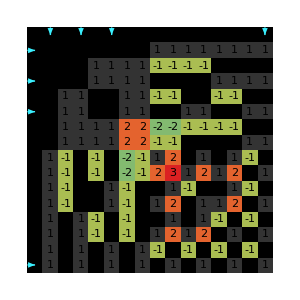
{-Graphics-,(0 | 0 | 0 | 1
0 | 0 | 1 | 1
0 | 1 | 0 | 1
1 | 1 | 1 | 1)}

```mathematica
matrixPicture[unavoidablyManySelfComp4]
```

Shit, product of symmetric permutations is only symmetric if they commute. The following function gives actual symmetric permutations of rows of a given (presumably symmetric) matrix:

```mathematica
symPermutations[B01_]:=Select[B01.PermutationMatrix[#]&/@Permutations[Range@Length@B01],SymmetricMatrixQ]
```

```mathematica
(selfCompatibleCount/@symPermutations[#])&/@allSymInvertible[3]
```

{{6,6,6,4},{6},{6},{6},{6},{6},{6},{6},{4,4,4,4},{4,6},{6},{4,6},{6},{6},{6},{6},{6},{6},{6},{6},{6},{4,6},{6}}

```mathematica
(selfCompatibleCount/@symPermutations[#])&/@allSymInvertible[2]
```

{{3,3},{3},{3}}

```mathematica
(selfCompatibleCount/@symPermutations[#])&/@allSymInvertible[1]
```

{{2}}

```mathematica
SortBy[Tally[Sort[selfCompatibleCount/@symPermutations[#]]&/@allSymInvertible[4]],#[[1,1]]&]
```

{{{5,5,5,5},4},{{5,9,9,9},4},{{5,5,5,5,5,5,5,5,5,5},1},{{5,9,9,9,9,9,9,9,9,9},1},{{6},24},{{6,8},12},{{6,6,6,8},8},{{9},144},{{9,9},30},{{10},96},{{10,10},48}}

```mathematica
correctSymPermSelfCompCount5=SortBy[Tally[ParallelMap[Sort[selfCompatibleCount/@symPermutations[#]]&,allSymInvertible[5]]],#[[1,1]]&]
```

{{{6,6},30},{{6,8},120},{{6,6,6,6},20},{{6,8,8,8,8,8},12},{{6,10,10,10,10,10},12},{{6,6,6,6,6,6,6,6},10},{{6,6,6,8,8,8,8,8,8,10},10},{{6,12,12,12,12,12,12,18,18,18},5},{{6,12,12,12,12,12,12,12,12,12,12,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14},1},{{6,12,12,12,12,12,12,12,12,12,12,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18},1},{{7,9},60},{{7,9,9,9},60},{{8},240},{{8,12},240},{{8,8,8,10},20},{{8,8,8,12},20},{{8,12,12,12},30},{{8,8,8,12,12,12,12,12},10},{{9},120},{{10},120},{{10,10},60},{{10,12},240},{{11},720},{{12},1320},{{12,12},420},{{12,14},120},{{12,16},240},{{12,18},240},{{12,24},60},{{12,12,12,12},80},{{12,18,18,18},20},{{12,12,12,12,14,14,14,14,14,14},5},{{13},840},{{13,17},240},{{14},240},{{15},120},{{15,19},300},{{15,19,19,19},60},{{16},120},{{16,20},120},{{16,16,20,20},30},{{17},1080},{{17,17},60},{{18},2040},{{18,18},210},{{19},3120},{{20},840},{{20,20},120}}

Guarantied lower bound from permutations looks (below) look line Binomial[n+1,Floor[(n+1)/2]]

```mathematica
{1->2,2->3,3->6,4->10,5->20}
```

```mathematica
Table[Binomial[n,Floor[n/2]],{n,1,7}]
```

{1,2,3,6,10,20,35}

```mathematica
someAnavoidablyLargeSelfCount5=Select[allSymInvertible[5],selfCompatibleCount/@symPermutations[#]=={20,20}&,10]
```

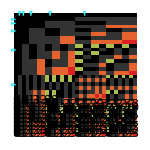
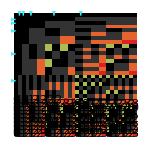
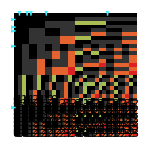
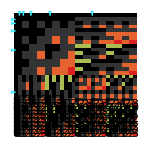
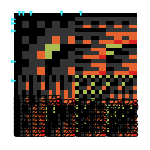
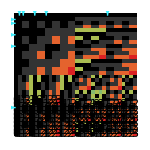
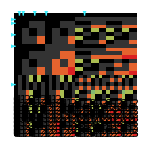
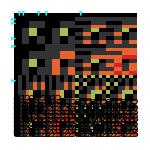
{{-Graphics-,(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)},-Graphics-}
{{-Graphics-,(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1)},-Graphics-}
{{-Graphics-,(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)},-Graphics-}
{{-Graphics-,(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0)},-Graphics-}
{{-Graphics-,(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1)},-Graphics-}
{{-Graphics-,(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0)},-Graphics-}
{{-Graphics-,(0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)},-Graphics-}
{{-Graphics-,(0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1)},-Graphics-}
{{-Graphics-,(0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)},-Graphics-}
{{-Graphics-,(0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1)},-Graphics-}Some 5×5 matrices unavoidably producing 20 self-compatible vectors (two sym perms for each)

```mathematica
Labeled[Column[Style[{matrixPicture[#]/.(ImageSize->_)->(ImageSize->150),Graph[setGraphStyle@dispFact@hasseSymFact@#,ImageSize->250]},Background->Black]&/@someAnavoidablyLargeSelfCount5],Style["Some 5×5 matrices unavoidably producing 20 self-compatible vectors (two sym perms for each)",White,Background->Black],Top]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"some-unavoidably-large-self-comp-5.jpg"}],%,Background->Black];
```

The last two are quite dissapointing:

```mathematica
Table[Sort[selfCompatibleCount/@symPermutations[m]],{m,{{{0, 0, 1}, {0, 1, 0}, {1, 0, 1}},{{0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 1, 0}, {1, 0, 0, 1}},{{0, 0, 0, 0, 1}, {0, 0, 0, 1, 0}, {0, 0, 1, 0, 0}, {0, 1, 0, 1, 0}, {1, 0, 0, 0, 1}},{{0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 1, 1, 0, 0}, {0, 1, 0, 0, 1, 0}, {1, 0, 0, 0, 0, 1}},{{0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 1, 0, 1, 0, 0}, {0, 1, 0, 0, 0, 1, 0}, {1, 0, 0, 0, 0, 0, 1}},{{0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 1, 0, 0, 0}, {0, 0, 1, 0, 0, 1, 0, 0}, {0, 1, 0, 0, 0, 0, 1, 0}, {1, 0, 0, 0, 0, 0, 0, 1}}}}]
```

{{6},{10,10},{20,20},{35,35,35,35},{66,66,66,70},{110,110,110,126,126,126,126,126,126,126}}

```mathematica
Table[Sort[selfCompatibleCount/@symPermutations[m]],{m,{{{0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0}, {1, 1, 0, 0, 0, 0, 0}}}}]
```

{{44,56,62,62,62,66,66,66}}

Trying to find the structure of a matrix that unavoidably produces Binomial[n,n/2] self compatible 0-1 vectors

```mathematica
manydiagMatr[sz_,diagPos_]:=Total[Table[Reverse[DiagonalMatrix[Table[1,sz-Abs[p]],p]],{p,diagPos}]]
```

```mathematica
Select[manydiagMatr[7,#]&/@(Prepend[0]/@Subsets[Range[6]]),selfCompatibleCount/@symPermutations[#]=={70}&]
```

{{{0,0,0,0,0,0,1},{0,0,0,0,0,1,0},{0,0,0,0,1,0,1},{0,0,0,1,0,1,0},{0,0,1,0,1,0,1},{0,1,0,1,0,1,0},{1,0,1,0,1,0,1}},{{0,0,0,0,0,0,1},{0,0,0,0,0,1,1},{0,0,0,0,1,1,1},{0,0,0,1,1,1,1},{0,0,1,1,1,1,1},{0,1,1,1,1,1,1},{1,1,1,1,1,1,1}}}

```mathematica
MatrixForm/@%
```

{(0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1 | 0 | 1),(0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1)}

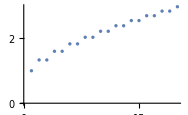

```mathematica
ListPlot[Table[2^n/Binomial[n+1,Floor[(n+1)/2]],{n,1,20}]]
```

```mathematica
(selfCompatibleCount/@symPermutations[#])&/@((manydiagMatr[#,Range[0,#-1]]&)/@Range[8])
```

{{2},{3},{6},{10},{20},{35},{70},{126}}

```mathematica
exportBlackBack[file_,expr_]:=Export[FileNameJoin@{NotebookDirectory[],file},expr,Background->Black]
```

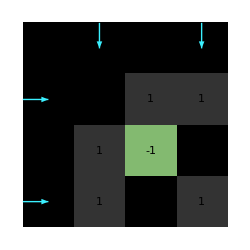
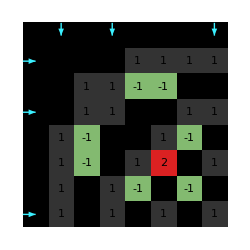
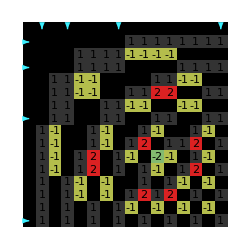
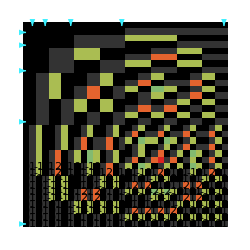
{{-Graphics-,(0 | 1
1 | 1)},-Graphics-}
{{-Graphics-,(0 | 0 | 1
0 | 1 | 1
1 | 1 | 1)},-Graphics-}
{{-Graphics-,(0 | 0 | 0 | 1
0 | 0 | 1 | 1
0 | 1 | 1 | 1
1 | 1 | 1 | 1)},-Graphics-}
{{-Graphics-,(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1)},-Graphics-}
{{-Graphics-,(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1)},-Graphics-}

```mathematica
With[{halfmatr=(manydiagMatr[#,Range[0,#-1]]&)/@Range[2,6]},Column[Style[{matrixPicture[#]/.(ImageSize->_)->(ImageSize->250),Graph[setGraphStyle@dispFact@hasseSymFact@#,ImageSize->250]},Background->Black]&/@halfmatr]]
```

```mathematica
exportBlackBack["half-matrix-demo.jpg",%];
```

```mathematica
matrixPicture[manydiagMatr[6,Range[0,5]][[-1;;1;;-1,-1;;1;;-1]]]
```

{-Graphics-,(1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)}

```mathematica
SeedRandom[42];With[{p=PermutationMatrix[RandomPermutation[5]],utr=manydiagMatr[5,Range[0,4]][[-1;;1;;-1,-1;;1;;-1]],m=MatrixForm},{p,utr//MatrixForm,p.utr//m,utr.p//m,p.utr.p//m,p.utr.(pᵀ)//m}]
```

{PermutationMatrix[…],(1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0),(1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1),(1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 0
0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0),(0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 1 | 1),(0 | 1 | 0 | 0 | 1
1 | 1 | 1 | 0 | 1
0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 1)}

Since conjugation by a permutation doesn’t effect the order and the self compatible count,

```mathematica
allSymInvDifCongClass[d_]:=With[{prms=PermutationMatrix/@Permutations[Range[d]]},DeleteDuplicatesBy[Select[(#+LowerTriangularize[#ᵀ,-1])&/@PadLeft/@(Internal`PartitionRagged[#,Range[d,1,-1]]&)/@Tuples[{0,1},(d(d+1))/2],MatrixRank@#==d&],First@MinimalBy[Table[p.#.(pᵀ),{p,prms}],Identity]&]]
```

```mathematica
allSymInvDifClassDifSort[d_]:=With[{prms=PermutationMatrix/@Permutations[Range[d]]},DeleteDuplicatesBy[DeleteDuplicatesBy[allSymInvertible[d],Sort[#ᵀ]&],First@MinimalBy[Table[p.#.(pᵀ),{p,prms}],Identity]&]](*deleting duplicates by sort of transpose is likely not needed*)
```

```mathematica
Length[allSymInvDifCongClass[#]]&/@Range[4]
```

{1,3,9,40}

```mathematica
Length[allSymInvertible@#]&/@Range[5]
```

{1,3,23,372,14206}

```mathematica
Length[allSymInvDifClassDifSort@#]&/@Range[4]
```

{1,2,6,27}

```mathematica
Length/@{{1},DeleteDuplicates[allSymInvertible[2],IsomorphicGraphQ[hasseSymFact@#1,hasseSymFact@#2]&],allThreeHasse,allFourHasse}
```

{1,1,3,7}

```mathematica
Diagonal[cube01[6].Inverse[manydiagMatr[6,Range[0,5]][[-1;;1;;-1,-1;;1;;-1]]].(cube01[6]ᵀ)]//Tally//SortBy[First]
```

{{-3,1},{-2,6},{-1,15},{0,20},{1,15},{2,6},{3,1}}

```mathematica
Diagonal[cube01[7].Inverse[manydiagMatr[7,Range[0,6]][[-1;;1;;-1,-1;;1;;-1]]].(cube01[7]ᵀ)]//
Tally//SortBy[First]
```

{{-3,1},{-2,7},{-1,21},{0,35},{1,35},{2,21},{3,7},{4,1}}

```mathematica
manydiagMatr[7,Range[0,6]][[-1;;1;;-1,-1;;1;;-1]]//Inverse//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 1 | -1 | 0
0 | 0 | 0 | 1 | -1 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0
1 | -1 | 0 | 0 | 0 | 0 | 0)

```mathematica
Select[allSymInvertible[4],IsomorphicGraphQ[Graph[1->2],hasseSymFact@#]&]
```

{{{0,0,1,1},{0,1,0,1},{1,0,0,1},{1,1,1,0}},{{0,0,1,1},{0,1,1,0},{1,1,0,1},{1,0,1,0}},{{0,1,0,1},{1,0,1,1},{0,1,1,0},{1,1,0,0}},{{0,1,1,1},{1,0,0,1},{1,0,1,0},{1,1,0,0}},{{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}}}

```mathematica
matrixPicture/@%
```

{{-Graphics-,(0 | 0 | 1 | 1
0 | 1 | 0 | 1
1 | 0 | 0 | 1
1 | 1 | 1 | 0)},{-Graphics-,(0 | 0 | 1 | 1
0 | 1 | 1 | 0
1 | 1 | 0 | 1
1 | 0 | 1 | 0)},{-Graphics-,(0 | 1 | 0 | 1
1 | 0 | 1 | 1
0 | 1 | 1 | 0
1 | 1 | 0 | 0)},{-Graphics-,(0 | 1 | 1 | 1
1 | 0 | 0 | 1
1 | 0 | 1 | 0
1 | 1 | 0 | 0)},{-Graphics-,(0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0)}}

```mathematica
dispFact/@(hasseSymFact/@(Table[1,{#},{#}]-IdentityMatrix[#]&/@Range[2,5]))
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Select[allSymInvertible[5],IsomorphicGraphQ[Graph[1->2],hasseSymFact@#]&,10]
```

{{{0,0,0,1,1},{0,0,1,0,1},{0,1,1,1,0},{1,0,1,1,0},{1,1,0,0,1}},{{0,0,0,1,1},{0,0,1,1,0},{0,1,1,0,1},{1,1,0,1,0},{1,0,1,0,1}},{{0,0,0,1,1},{0,1,1,0,1},{0,1,0,1,0},{1,0,1,1,0},{1,1,0,0,1}},{{0,0,0,1,1},{0,1,1,1,0},{0,1,0,0,1},{1,1,0,1,0},{1,0,1,0,1}},{{0,0,1,0,1},{0,0,1,1,0},{1,1,1,0,0},{0,1,0,1,1},{1,0,0,1,1}},{{0,0,1,0,1},{0,1,0,1,1},{1,0,1,1,0},{0,1,1,0,0},{1,1,0,0,1}},{{0,0,1,0,1},{0,1,1,1,0},{1,1,1,0,0},{0,1,0,0,1},{1,0,0,1,1}},{{0,0,1,1,0},{0,1,0,1,1},{1,0,1,0,1},{1,1,0,1,0},{0,1,1,0,0}},{{0,0,1,1,0},{0,1,1,0,1},{1,1,1,0,0},{1,0,0,1,1},{0,1,0,1,0}},{{0,0,1,1,1},{0,1,0,0,1},{1,0,0,1,1},{1,0,1,0,1},{1,1,1,1,0}}}

```mathematica
MatrixForm/@%
```

{(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1),(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1),(0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1),(0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1),(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1),(0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1),(0 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1),(0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0),(0 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 1
1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 1
0 | 1 | 0 | 1 | 0),(0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)}

```mathematica
<<"C:\\Users\\mitya\\Documents\\WolframPlay\\Correlating-Vectors-Research\\all-sym-hasse-5.mx"
```

```mathematica
<<"C:\\Users\\mitya\\Documents\\WolframPlay\\Correlating-Vectors-Research\\all-sym-hasse-4.mx"
```

```mathematica
<<"C:\\Users\\mitya\\Documents\\WolframPlay\\Correlating-Vectors-Research\\all-sym-hasse-3.mx"
```

```mathematica
Length/@{allThreeHasse,allFourHasse,allFiveHasse}
```

{3,7,35}

```mathematica
addGraphProps/@hasseSymFact/@allSymInvertible[2]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
allSymInvertible[5]//Length//AbsoluteTiming
```

{1.785,14206}

```mathematica
graphFull[B01_]:=Module[{d=Length@B01,cube,matr},cube=Tuples[{0,1},d];matr=(cube.Inverse@B01.(cubeᵀ))/.{1->0,x_/;x!=0->2};
Flatten@Table[If[i!=j&&And@@NonNegative[matr[[i]]-matr[[j]]]&&And@@NonNegative[matr[[All,i]]-matr[[All,j]]],cube[[i]]->cube[[j]],Nothing],{i,2^d},{j,2^d}]]
```

```mathematica
graphFactorizedRaw[B01_]:=Module[{d=Length@B01,cube,filtprodmatr,grps,filt=(#/.{1->0,x_/;x!=0->2}&)},cube=Tuples[{0,1},d];filtprodmatr=filt[cube.Inverse[B01].(cubeᵀ)];grps={(p|->cube[[p]])/@#,{filtprodmatr[[#[[1]]]],filtprodmatr[[All,#[[1]]]]}}&/@GatherBy[Range[2^d],{filtprodmatr[[#]],filtprodmatr[[All,#]]}&];
Flatten@Table[If[i!=j&&And@@Flatten[NonNegative[grps[[i,2]]-grps[[j,2]]]],grps[[i,1]]->grps[[j,1]],Nothing],{i,Length@grps},{j,Length@grps}]]
addGrProps[gr_]:=Module[{filt=(#/.{1->0,x_/;x!=0->2}&)},gr//IGVertexMap[Sqrt@*Length,"SqLength"->VertexList]/*IGVertexMap[Length,"Length"->VertexList]/*IGVertexMap[MatrixForm[#ᵀ]&,Tooltip->VertexList]]
grFact[B01_]:=addGrProps[Graph[graphFactorizedRaw[B01],PerformanceGoal->"Quality"]]
hasseFact[B01_]:=addGrProps[hasseDiagram@Graph[graphFactorizedRaw[B01],PerformanceGoal->"Speed"]]
```

```mathematica
dispFact[hasseFact@IdentityMatrix[3]]
```

-Graphics-

```mathematica
bruteAllInv[d_]:=Select[Partition[#,d]&/@Tuples[{0,1},d^2],MatrixRank@#==d&]
```

```mathematica
DeleteDuplicates[dispFact/@hasseFact/@bruteAllInv[2],IsomorphicGraphQ]
```

{-Graphics-,-Graphics-}

```mathematica
DeleteDuplicates[dispFact/@hasseFact/@bruteAllInv[3],IsomorphicGraphQ]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{prms=PermutationMatrix/@Permutations[Range[4]],grps},grps=GroupBy[bruteAllInv[4],Sort/@Total/@{#,#ᵀ}&]]
```

Two matrices that are non equivalent but have the same set of sums of rows and columns

```mathematica
MatrixForm/@{{{0,0,0,1},{0,0,1,0},{0,1,0,1},{1,0,1,0}},{{1,1,0,0},{1,0,1,0},{0,1,0,0},{0,0,0,1}}}
```

{(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0),(1 | 1 | 0 | 0
1 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)}

Indeed:

```mathematica
With[{perms=PermutationMatrix/@Permutations@Range[4]},MemberQ[Flatten[Table[p1.{{0,0,0,1},{0,0,1,0},{0,1,0,1},{1,0,1,0}}.p2,{p1,perms},{p2,perms}],1],{{1,1,0,0},{1,0,1,0},{0,1,0,0},{0,0,0,1}}]]
```

False

```mathematica
Union[selfCompatibleCount/@bruteAllInv[4]]
```

{5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
Select[bruteAllInv[4],selfCompatibleCount@#==16&,5]
```

{{{0,0,0,1},{0,1,0,0},{1,1,1,1},{0,1,1,1}},{{0,0,0,1},{0,1,1,1},{1,0,1,1},{0,0,1,1}},{{0,0,0,1},{1,1,0,1},{0,1,1,1},{0,1,0,1}},{{0,0,0,1},{1,1,0,1},{1,1,1,1},{0,1,0,1}},{{0,0,0,1},{1,1,1,1},{0,0,1,0},{0,1,1,1}}}

```mathematica
expSelfComp={{0,0,0,1},{0,1,0,0},{1,1,1,1},{0,1,1,1}};
```

```mathematica
With[{prms=PermutationMatrix/@Permutations@Range[4]},Union[selfCompatibleCount/@Flatten[Table[p1.expSelfComp.p2,{p1,prms},{p2,prms}],1]]]
```

{9,10,11,12,13,14,16}

```mathematica
NestWhile[randomInvertible[5]&,{{1}},selfCompatibleCount@#<30&]
```

{{1,0,0,0,0},{0,0,1,0,0},{1,0,0,0,1},{1,1,0,0,1},{1,0,1,1,0}}

Examples of 5×5 matrices resulting in large self compatible count with various sizes of minimal achievable by permutation counts

```mathematica
{{0,0,1,1,0},{1,1,0,1,1},{0,1,1,1,0},{0,1,1,1,1},{1,1,1,1,1}}
```

```mathematica
{{1,1,0,0,1},{1,1,1,1,1},{1,0,1,1,1},{1,0,1,1,0},{1,0,0,1,0}}
```

```mathematica
{{0,1,0,1,1},{0,1,0,0,0},{0,0,0,0,1},{1,1,1,1,1},{1,1,0,1,1}}
```

```mathematica
{{1,0,0,0,0},{0,0,1,0,0},{1,0,0,0,1},{1,1,0,0,1},{1,0,1,1,0}}
```

```mathematica
With[{prms=PermutationMatrix/@Permutations@Range[5]},Union[selfCompatibleCount/@Flatten[Table[p1.{{1,0,0,0,0},{0,0,1,0,0},{1,0,0,0,1},{1,1,0,0,1},{1,0,1,1,0}}.p2,{p1,prms},{p2,prms}],1]]]
```

{16,18,19,20,21,22,23,24,25,26,28,30}

```mathematica
dispFact@hasseFact@{{1,0,0,0,0},{0,0,1,0,0},{1,0,0,0,1},{1,1,0,0,1},{1,0,1,1,0}}
```

-Graphics-

```mathematica
dispFact@hasseFact@{{0,1,0,1,1},{0,1,0,0,0},{0,0,0,0,1},{1,1,1,1,1},{1,1,0,1,1}}
```

-Graphics-

Lists of self-compatible counts achivable by permutations of rows and columns:

```mathematica
With[{prms=PermutationMatrix/@Permutations@Range[3]},Union/@Map[selfCompatibleCount,GatherBy[bruteAllInv[3],MinimalBy[Flatten[Table[p1.#.p2,{p1,prms},{p2,prms}],1],Identity]&],{2}]]
```

{{4,6,7},{5,6,7},{6,7},{6,7},{5,6,7},{5,6,7,8},{4},{4,6,7,8}}

```mathematica
With[{prms=PermutationMatrix/@Permutations@Range[4]},Union/@Map[selfCompatibleCount,GatherBy[bruteAllInv[4],MinimalBy[Flatten[Table[p1.#.p2,{p1,prms},{p2,prms}],1],Identity]&],{2}]]
```